```mathematica
l0[x_] =((x - 2)*(x - 4)*(x - 6))/-15
```

-1/15 (-6+x) (-4+x) (-2+x)

```mathematica
l1[x_] = ((x - 1)*(x - 4)*(x - 6))/((2 -1)*(2 - 4)*(2 - 6))
```

1/8 (-6+x) (-4+x) (-1+x)

```mathematica
l2[x_] = ((x - 1)*(x - 2)*(x - 6))/((4 - 1)*(4 -2)*(4 - 6))
```

-1/12 (-6+x) (-2+x) (-1+x)

```mathematica
l3[x_] = ((x - 1)*(x - 2)*(x - 4))/((6 - 1)*(6 - 2)*(6 - 4))
```

1/40 (-4+x) (-2+x) (-1+x)

```mathematica
p[x_] = 2*l0[x] + 9*l1[x] + 41*l2[x] + 97*l3[x]
```

-2/15 (-6+x) (-4+x) (-2+x)+9/8 (-6+x) (-4+x) (-1+x)-41/12 (-6+x) (-2+x) (-1+x)+97/40 (-4+x) (-2+x) (-1+x)

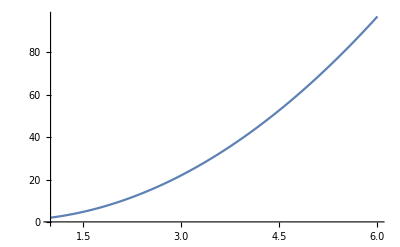

```mathematica
plotMain = Plot[p[x],{x, 1, 6}]
```